```mathematica
StandardDeviation[{1,2,3}]
```

1

```mathematica
StandardDeviation[{2,3,4}]
```

1

```mathematica
N@StandardDeviation[Range[12]]
```

3.60555

```mathematica
v2[l_List]:=With[{m=Mean@l,c=Length@l},
l-Table[m,{c}]]
```

```mathematica
v2[{1,2,3}].v2[{1,2,3}]
```

2

```mathematica
v2[{2,3,4}].v2[{2,3,4}]
```

2

```mathematica
StandardDeviation[Abs@{x1,x2,x3}]//Simplify
```

(√(Abs[x1]^2+Abs[x2]^2-Abs[x2] Abs[x3]+Abs[x3]^2-Abs[x1] (Abs[x2]+Abs[x3])))/(√3)

```mathematica
Remove[cheapGaussian];
cheapGaussian[n_,mean_,sigma_]:=
With[{r2=Sqrt[12.0n]},
Module[{r=0},
For[i=0,i<n,i++,
r+=(r2(RandomReal[]-0.5))];
(sigma*r)/n+mean]]
```

```mathematica
N[Sqrt[12.0], 15]
```

3.4641

```mathematica
NumberForm[3.4641016151377544,16]
```

3.464101615137754

```mathematica
Remove[cheaperGaussian];
cheaperGaussian[mean_, sigma_]:=
With[{g=RandomReal[{-1,1}]+RandomReal[{-1,1}]+RandomReal[{-1,1}]},
g*sigma+mean]
```

function rnd_bmt() {
	var x = 0, y = 0, rds, c;
	// Get two random numbers from -1 to 1.
	// If the radius is zero or greater than 1, throw them out and pick two new ones
	// Rejection sampling throws away about 20% of the pairs.
	do {
	x = Math.random()*2-1;
	y = Math.random()*2-1;
	rds = x*x + y*y;
	}
	while (rds == 0 || rds > 1)
	// This magic is the Box-Muller Transform
	c = Math.sqrt(-2*Math.log(rds)/rds);
	// It always creates a pair of numbers. I'll return them in an array. 
	// This function is quite efficient so don't be afraid to throw one away if you don't need both.
	return [x*c, y*c];
}

```mathematica
Remove[BoxMuller];
BoxMuller[m_,s_]:=
Module[{x=RandomReal[{-1,1}],y=RandomReal[{-1,1}],
rds,c},
rds=x*x+y*y;
While[rds===0||rds>1,
x=RandomReal[{-1,1}];
y=RandomReal[{-1,1}];
rds=x*x+y*y];
c=Sqrt[-2*Log[rds]/rds];
m+s*x*c
]
```

```mathematica
testStats[l_,n_,m_,s_]:=With[{ts={
Timing@Table[cheapGaussian[n,m,s],{l}],
Timing@Table[RandomReal[NormalDistribution[m,s]],{l}],
Timing@Table[cheaperGaussian[m,s],{l}],
Timing@Table[BoxMuller[m,s],{l}]
}},
With[{results={#⟦1⟧,Mean@#⟦2⟧,StandardDeviation@#⟦2⟧}&/@ts,
testLabels={"cheap","MMA","cheaper","BoxMuller"},
columnLabels={"test","time","mean","stddev"}},
Prepend[
Prepend[results//Transpose,testLabels]//Transpose,
columnLabels]]];
```

```mathematica
testStats[100000,4,2,5.3]//MatrixForm
```

(test | time | mean | stddev
cheap | 1.04688 | 2.00174 | 5.30466
MMA | 0.015625 | 1.98719 | 5.28699
cheaper | 0.21875 | 2.01562 | 5.30525
BoxMuller | 1.17188 | 1.98941 | 5.29426)

```mathematica
testPlot[l_,n_,m_,s_]:=Histogram[{
Table[cheapGaussian[n,m,s],{l}],
Table[RandomReal[NormalDistribution[m,s]],{l}],
Table[cheaperGaussian[m,s],{l}],
Table[BoxMuller[m,s],{l}]
}]
```

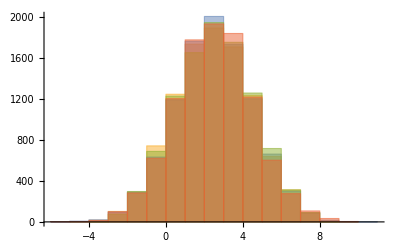

```mathematica
testPlot[10000,5,2.5,2]
```

```mathematica
testStats[100000,4,0,1]//MatrixForm
```

(test | time | mean | stddev
cheap | 1.04688 | 0.0033607 | 1.00077
MMA | 0. | -0.00470024 | 1.00254
cheaper | 0.203125 | -0.00187336 | 1.00445
BoxMuller | 1.15625 | 0.00551901 | 0.997774)

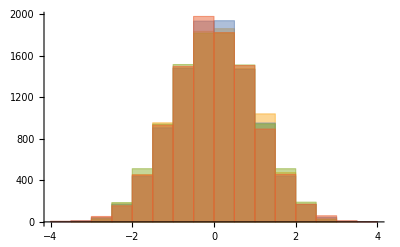

```mathematica
testPlot[10000,4,0,1]
```

```mathematica
Histogram@{1.112272,0.608056,-0.712082,-1.718945,-0.400054,-2.271720,0.866331,-1.032577,-0.358203,-1.113812,0.047448,0.844847,2.224139,-0.006417,-0.749836,0.154229,-0.227977,-1.328406,0.054193,-1.062037,0.786889,-0.069550,-1.704961,-0.641019,0.155588,0.038588,-0.105514,0.319236,-0.891123,1.317130,0.505623,-0.159352,0.973994,-0.242362,-1.074005,0.528939,0.396976,-0.111086,-0.394803,0.264499,-0.092298,1.940762,0.799445,1.011509,-0.290069,-0.834082,1.417492,-0.028241,1.538078,1.338815,-0.763600,0.493948,-0.703911,-0.350579,-0.693822,-0.662066,-0.672263,0.833918,0.075808,0.687660,0.039353,-0.158962,0.438268,0.359203,-1.119531,-2.054421,2.230583,0.297586,0.192773,0.203833,1.353821,0.069704,2.094660,-0.348901,0.746676,0.616053,1.153809,-0.721999,-0.644426,-1.192861,0.010962,-1.750443,0.338185,-0.754630,0.665290,-0.437011,-1.689422,0.623377,2.032396,-0.178548,0.577086,0.116111,-0.740394,1.413952,-0.520030,1.361777,1.193530,0.649530,0.531032,0.795070}
```

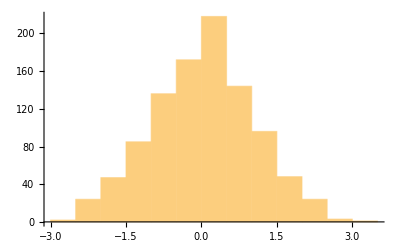

```mathematica
{1.112272,0.608056,-0.712082,-1.718945,-0.400054,-2.271720,0.866331,-1.032577,-0.358203,-1.113812,0.047448,0.844847,2.224139,-0.006417,-0.749836,0.154229,-0.227977,-1.328406,0.054193,-1.062037,0.786889,-0.069550,-1.704961,-0.641019,0.155588,0.038588,-0.105514,0.319236,-0.891123,1.317130,0.505623,-0.159352,0.973994,-0.242362,-1.074005,0.528939,0.396976,-0.111086,-0.394803,0.264499,-0.092298,1.940762,0.799445,1.011509,-0.290069,-0.834082,1.417492,-0.028241,1.538078,1.338815,-0.763600,0.493948,-0.703911,-0.350579,-0.693822,-0.662066,-0.672263,0.833918,0.075808,0.687660,0.039353,-0.158962,0.438268,0.359203,-1.119531,-2.054421,2.230583,0.297586,0.192773,0.203833,1.353821,0.069704,2.094660,-0.348901,0.746676,0.616053,1.153809,-0.721999,-0.644426,-1.192861,0.010962,-1.750443,0.338185,-0.754630,0.665290,-0.437011,-1.689422,0.623377,2.032396,-0.178548,0.577086,0.116111,-0.740394,1.413952,-0.520030,1.361777,1.193530,0.649530,0.531032,0.795070,0.068308,-0.358846,0.279216,-0.825729,1.514888,0.975050,0.956658,-0.565800,0.983572,-1.317465,1.025532,-0.739739,-0.561385,0.398978,1.421916,-0.281802,-0.066793,-0.758029,1.123406,-0.123306,-0.035955,-0.955746,0.424727,2.504125,0.761803,-0.608903,-0.004104,-0.940890,-0.199273,0.764977,0.401386,-0.050068,-1.087452,0.656803,-0.787853,-0.896929,-0.267121,-0.117406,0.560530,0.726328,-0.045020,0.881899,0.088578,1.592211,1.153822,-1.146073,1.351560,0.699798,-0.346182,0.679158,-0.619505,-1.468767,-0.816706,-1.293842,0.254315,-0.223905,1.831796,-0.963918,2.495719,1.185442,-0.335046,-0.090862,2.376596,1.692307,-0.510496,-0.102639,0.848346,-0.325517,-0.526729,0.091235,-0.723942,0.404099,-0.707537,-1.242314,-0.722322,0.914348,-1.288773,-1.823213,-1.348927,0.114548,0.034483,-1.488894,-0.885555,-1.281798,0.101309,0.586722,1.127835,0.116007,1.272190,0.463667,-0.865309,1.027673,-0.422640,-1.186035,1.757239,-0.881090,0.397605,-1.043040,0.350256,1.082079,0.127035,-1.228323,0.955383,-0.799682,1.078941,0.105292,0.086902,-0.317178,1.243362,0.462748,0.995733,0.684553,0.632054,-1.483983,-0.111702,0.314690,0.827008,-1.381291,1.135649,0.128214,0.077597,1.897722,1.274028,-1.009459,0.014621,1.188898,2.097350,-1.082957,-1.474850,0.304736,2.144068,-0.008507,1.703779,-0.685729,0.204364,1.688990,-0.201264,0.334366,-2.026049,-1.509851,0.639876,-1.329092,0.734795,0.413275,-1.680969,2.005727,0.470151,-0.349571,0.238787,-1.305039,-0.505716,1.739437,1.675375,-0.674247,0.382256,0.519472,-1.268328,-0.060277,0.096453,-0.800224,0.866380,0.423061,-0.187666,0.964759,0.196311,-0.847418,-0.503992,0.437977,-0.453128,-0.540863,0.176554,-2.487141,-0.536647,-0.181852,0.283127,-0.490130,0.721034,-0.538643,-1.092353,1.210567,0.802274,-0.144424,0.610105,1.160018,0.617359,1.030782,0.510495,0.121693,-0.393553,0.127179,-0.213400,0.312730,2.540210,0.813230,0.741053,-1.361772,0.027618,0.560958,-1.447772,-0.835187,1.367298,-0.410744,1.237834,-0.754738,-1.125063,1.071543,-1.229884,0.092173,-0.858164,-0.794052,0.880561,0.127165,-1.387502,-0.198658,-1.028641,1.334652,-0.062900,-1.383439,-0.269446,1.521237,0.123801,-0.151250,0.526535,0.156911,-0.152974,-0.798050,0.948370,0.217614,-1.060497,-1.502538,1.148002,0.270071,-0.709758,-0.880592,0.391143,2.043008,-0.152192,0.319077,-0.562178,-0.462700,-0.169356,-1.795396,-1.063690,1.041801,0.110085,-1.675745,0.964282,0.982439,1.245800,1.244876,-0.235973,1.219867,0.025848,0.281562,1.394315,0.301730,0.082778,1.442322,-0.651636,0.703421,-1.025594,-0.315745,-0.154334,-0.905295,0.153762,-1.531038,-0.760158,0.837440,0.474942,1.467141,0.438415,1.343880,0.723813,-0.205487,-1.093274,-0.975532,0.278006,-0.383665,0.233441,0.752911,-1.266156,-0.698800,0.156303,0.893387,0.762104,-2.478172,-0.732940,-1.524273,-0.382646,1.658757,-0.063953,-0.582248,-0.608750,1.071060,0.434734,-0.133190,0.595515,-0.393411,0.258824,1.177917,-2.109904,-0.645317,1.778641,0.015119,-0.612071,1.832691,-1.216541,-1.182660,0.527355,-0.145855,0.179337,-1.095629,-0.195621,0.670011,-0.320036,-0.168781,0.088322,-0.455647,-1.608781,-2.401462,-0.512046,-0.614558,1.289659,-0.784856,-2.326257,0.345973,0.293057,1.042735,-0.505072,-0.195128,0.003433,-0.875842,0.740925,1.311699,0.674623,0.577756,0.444097,1.955065,-0.204814,-0.466416,0.915955,-0.808625,0.332745,-1.088312,0.382965,-1.727920,-0.318918,-0.258134,-0.146619,2.223084,-0.120008,-0.461945,-1.296104,0.704472,-1.542248,0.336945,0.018396,0.931518,0.049119,-1.135211,1.756250,0.504134,-1.238825,0.481668,-1.064658,-1.285527,0.332946,1.666411,0.153743,-1.512658,-1.465779,1.702667,-0.892060,0.801768,-0.899046,-2.209649,-1.680226,1.065791,0.165205,1.260209,0.177021,0.761657,1.113550,0.184506,0.334785,0.091629,1.483838,0.763832,0.359269,0.764523,1.330244,0.114318,0.482053,-0.610943,1.461531,-1.061174,0.943057,-1.360213,0.365818,-1.535585,1.042114,0.484779,2.178055,1.629694,-1.641281,-1.782559,-0.828050,0.386431,-0.615129,0.126237,-0.759533,-1.121869,1.310914,2.170419,0.683200,1.263389,0.541845,1.200609,0.441811,-0.161925,-2.133274,0.182952,-0.525905,-0.729872,-0.472729,2.079212,-1.999914,1.258554,1.763695,1.643535,-2.057810,0.715784,0.852509,-0.770665,0.247261,0.579894,1.566527,-2.434058,0.773689,0.748167,0.614496,0.274732,-0.479045,1.562587,-0.747445,-1.974283,0.642930,-0.535461,-1.845580,-0.319560,0.087460,0.562893,1.559105,0.961801,-2.702220,-0.102159,-0.497645,1.653413,0.366434,0.141148,2.254678,-2.053488,-0.466800,0.337505,2.090819,2.225365,0.013604,-0.692335,0.466069,0.756636,0.223024,3.410518,-0.450792,0.973615,1.149031,-0.077052,1.133451,-2.203196,-0.872285,-1.456439,-0.081539,1.844215,0.663388,0.141634,0.856582,-0.149386,-0.944042,0.820569,0.069266,1.001687,-0.670093,-0.597876,1.073813,0.489935,-0.164578,1.103554,-1.516928,1.707243,0.001877,0.669363,-1.701693,1.044386,-1.391563,-0.983646,0.604500,0.535349,-0.650070,1.395619,0.267438,-0.557318,0.468165,0.135737,1.778431,-0.056908,-0.142189,0.422525,-1.057476,-1.163406,-0.581952,0.909585,-2.006322,-0.065450,0.163398,-1.018080,1.540204,0.606546,-0.404258,0.732413,-0.242026,1.338558,-0.042884,-0.240128,0.342241,-0.164038,-0.418520,-1.545149,0.184752,2.198051,0.096401,0.490663,-0.462090,-0.253829,1.023470,-0.499378,-0.202681,0.368835,-0.298910,0.509365,-0.661707,-0.200066,-0.239780,0.332859,0.413734,-0.297059,0.470469,2.313138,-0.637597,-0.154665,-0.493859,-1.184475,-1.982100,-1.551146,0.359814,1.735541,-1.511103,-0.113009,0.201948,-0.436620,-0.582853,-0.878154,-0.361659,1.010387,-0.783001,0.415705,-0.085881,0.284570,0.538641,0.930150,1.283181,0.946303,0.459370,-0.648625,0.243834,-1.320477,-0.229951,-0.636441,-0.398299,0.116659,-0.881253,-0.972818,-0.026632,0.887271,-0.370001,-0.714481,-0.782909,0.406679,-0.889621,-0.332799,-2.360327,2.438322,0.197292,0.227117,1.875729,1.064490,-0.769251,-0.212866,0.106145,-0.729878,-1.017207,-2.017866,-2.067834,-0.570762,-0.434269,-0.113130,1.062918,-2.491158,-1.749018,0.485219,-0.921498,1.677916,0.124473,-0.058009,0.101314,-0.694956,0.255646,-0.166965,1.557410,0.463916,-0.970993,0.304052,0.863534,0.325858,1.379988,0.651288,-0.565573,-0.471485,0.246246,-0.067688,-1.613035,-0.387326,-0.506457,0.131985,0.533433,1.144227,1.571290,0.612561,-1.676668,1.541457,0.102637,0.696445,0.144644,-0.710858,0.908874,0.290309,1.509513,-1.033397,-0.449716,0.562817,0.145174,-0.005054,0.818894,-0.325694,0.731742,0.284128,0.601317,-1.558509,0.296207,0.188980,-1.201184,-0.808029,0.088832,0.008091,-0.093955,-0.530967,0.401385,1.060757,-1.524652,-0.198556,0.351099,0.447791,1.185444,1.361814,0.430592,0.244231,0.335704,-0.404243,1.351340,0.214246,0.746036,0.497282,-0.589985,1.192560,-0.485115,1.261105,-1.949673,-0.346076,0.046646,-1.332821,0.650532,-0.594524,1.080372,-0.361096,-0.210992,0.819858,1.821696,-0.557135,-0.349194,-0.707122,-0.836168,0.030684,-0.039542,-0.307551,-1.323532,0.114815,0.915413,-0.453989,2.278012,-1.046900,-0.215421,2.144849,-0.840004,0.334379,-1.953136,0.456308,0.373312,-0.370239,0.938276,1.808145,0.353710,-1.098864,0.194312,0.313950,0.642874,-0.300421,1.968607,-2.439561,-0.597582,0.610293,-0.499152,0.357962,1.483237,-0.316680,-0.776553,0.680279,-1.579734,0.040494,0.147215,1.061615,0.329627,-0.003387,-0.642778,-1.010713,0.542360,-0.830923,0.962900,-0.292201,0.866959,-0.587772,1.173389,0.727655,-1.561459,0.160282,-0.146652,0.675232,0.453106,-0.138674,-0.015172,0.584648,1.511314,-0.752653,0.336874,0.265320,-1.138027,-1.479686,-0.790524,1.960117,1.027907,1.182525,0.454026,0.098747,2.691294,-1.667661,-0.795761,-0.509465,0.201960,-0.700141,0.554854,1.417895,1.341917,0.365445,0.807383,-0.198966,0.366745,0.144994,-0.520452,-1.098171,-0.995497,1.932433,-0.041876,1.229131,-0.191117,-0.454016,-0.415251,-0.119090,-2.299955,-0.106447,0.309771,0.006282,0.097275,0.852884,-0.295465,-0.234021,0.326160,-0.861502,-0.450004,-1.150339,-1.683161,-1.858069,0.814332,0.269390,-1.804409,-0.140837,0.000061,1.111122,0.392502,-0.068954,0.153935,-1.125601,0.971562,1.914874,2.276473,-1.689056,-1.180125,0.709059,1.305839,1.503408,1.067323,0.077412,-2.076445,-1.047962,0.435488,-0.035124,0.199417,-1.165139,-0.176836,-1.932700,-1.143789,-0.601720,-1.281015,0.108325,-0.536475,-1.596664,1.621706,0.224151,1.114644,1.383195,0.077263,0.596430,1.074276,0.347524,0.621598,-1.231771,-1.194270,1.262019,0.473275,-0.081956,0.749296,-1.698931,0.303072,0.529865,1.198244,0.456618,1.605409,-0.438997,-1.030265,0.735516,-0.010639,-2.183039,-0.078976,-0.360609,0.261325,0.247640,-2.717432,0.602518,-1.053168,0.744190,0.802579,0.763083,-0.765801,-1.199015,0.302608,-0.197648,2.057648,-2.315334,1.234932,0.570399,-1.549787,0.692549,-0.685791,-1.044153}//Histogram
```

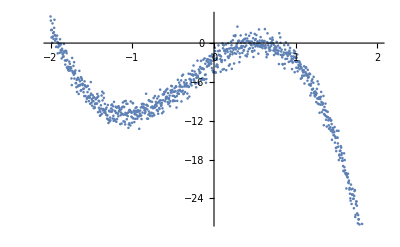

```mathematica
ListPlot[{{-2.000000,4.112272},{-1.995996,3.468333},{-1.991992,2.009302},{-1.987988,0.864377},{-1.983984,2.046035},{-1.979980,0.037960},{-1.975976,3.040427},{-1.971972,1.006757},{-1.967968,1.547189},{-1.963964,0.658457},{-1.959960,1.687409},{-1.955956,2.353315},{-1.951952,3.601927},{-1.947948,1.241500},{-1.943944,0.369021},{-1.939940,1.144831},{-1.935936,0.635175},{-1.931932,-0.591900},{-1.927928,0.664853},{-1.923924,-0.576425},{-1.919920,1.148252},{-1.915916,0.168358},{-1.911912,-1.589715},{-1.907908,-0.647642},{-1.903904,0.027884},{-1.899900,-0.209410},{-1.895896,-0.473020},{-1.891892,-0.166994},{-1.887888,-1.495296},{-1.883884,0.595795},{-1.879880,-0.332097},{-1.875876,-1.112681},{-1.871872,-0.094171},{-1.867868,-1.424590},{-1.863864,-2.369525},{-1.859860,-0.879107},{-1.855856,-1.122828},{-1.851852,-1.741884},{-1.847848,-2.135833},{-1.843844,-1.586002},{-1.839840,-2.051512},{-1.835836,-0.126408},{-1.831832,-1.374927},{-1.827828,-1.269311},{-1.823824,-2.676587},{-1.819820,-3.325548},{-1.815816,-1.178176},{-1.811812,-2.727366},{-1.807808,-1.263761},{-1.803804,-1.564997},{-1.799800,-3.768644},{-1.795796,-2.611592},{-1.791792,-3.909211},{-1.787788,-3.654905},{-1.783784,-4.096443},{-1.779780,-4.162253},{-1.775776,-4.269288},{-1.771772,-2.859219},{-1.767768,-3.712717},{-1.763764,-3.195531},{-1.759760,-3.937783},{-1.755756,-4.229327},{-1.751752,-3.724608},{-1.747748,-3.895470},{-1.743744,-5.465289},{-1.739740,-6.490554},{-1.735736,-2.295216},{-1.731732,-4.317173},{-1.727728,-4.510241},{-1.723724,-4.586732},{-1.719720,-3.523596},{-1.715716,-4.893865},{-1.711712,-2.954365},{-1.707708,-5.482687},{-1.703704,-4.471177},{-1.699700,-4.685177},{-1.695696,-4.230107},{-1.691692,-6.187916},{-1.687688,-6.191657},{-1.683684,-6.820723},{-1.679680,-5.696849},{-1.675676,-7.537524},{-1.671672,-5.527488},{-1.667668,-6.698219},{-1.663664,-5.355542},{-1.659660,-6.534414},{-1.655656,-7.862725},{-1.651652,-5.625159},{-1.647648,-4.290706},{-1.643644,-6.575553},{-1.639640,-5.893158},{-1.635636,-6.426713},{-1.631632,-7.355139},{-1.627628,-5.272058},{-1.623624,-7.276650},{-1.619620,-5.464801},{-1.615616,-5.702355},{-1.611612,-6.315013},{-1.607608,-6.501522},{-1.603604,-6.304850},{-1.599600,-7.098336},{-1.595596,-7.591572},{-1.591592,-7.018952},{-1.587588,-8.188703},{-1.583584,-5.912256},{-1.579580,-6.515632},{-1.575576,-6.596929},{-1.571572,-8.181663},{-1.567568,-6.693940},{-1.563564,-9.056000},{-1.559560,-6.773401},{-1.555556,-8.598449},{-1.551552,-8.479253},{-1.547548,-7.577429},{-1.543544,-6.612414},{-1.539540,-8.373442},{-1.535536,-8.215130},{-1.531532,-8.962452},{-1.527528,-7.136495},{-1.523524,-8.438079},{-1.519520,-8.404996},{-1.515516,-9.378451},{-1.511512,-8.051043},{-1.507508,-6.024109},{-1.503504,-7.818300},{-1.499499,-9.240279},{-1.495495,-8.686161},{-1.491491,-9.673037},{-1.487487,-8.980921},{-1.483483,-8.065585},{-1.479479,-8.477504},{-1.475475,-8.976703},{-1.471471,-10.061250},{-1.467467,-8.363579},{-1.463463,-9.854242},{-1.459459,-10.008749},{-1.455455,-9.423797},{-1.451451,-9.318368},{-1.447447,-8.684148},{-1.443443,-8.561497},{-1.439439,-9.375427},{-1.435435,-8.490526},{-1.431431,-9.325303},{-1.427427,-7.862565},{-1.423423,-8.341291},{-1.419419,-10.680967},{-1.415415,-8.222560},{-1.411411,-8.912996},{-1.407407,-9.997099},{-1.403403,-9.009334},{-1.399399,-10.345024},{-1.395395,-11.230769},{-1.391391,-10.614649},{-1.387387,-11.127183},{-1.383383,-9.613887},{-1.379379,-10.126430},{-1.375375,-8.104517},{-1.371371,-10.933485},{-1.367367,-7.506572},{-1.363363,-8.849043},{-1.359359,-10.401198},{-1.355355,-10.188154},{-1.351351,-7.751313},{-1.347347,-8.465699},{-1.343343,-10.698077},{-1.339339,-10.319278},{-1.335335,-9.396835},{-1.331331,-10.598727},{-1.327327,-10.827454},{-1.323323,-10.236496},{-1.319319,-11.078171},{-1.315315,-9.976121},{-1.311311,-11.113244},{-1.307307,-11.673006},{-1.303303,-11.177498},{-1.299299,-9.564813},{-1.295295,-11.791423},{-1.291291,-12.348858},{-1.287287,-11.897073},{-1.283283,-10.455609},{-1.279279,-10.557195},{-1.275275,-12.101606},{-1.271271,-11.518817},{-1.267267,-11.935126},{-1.263263,-10.571604},{-1.259259,-10.105296},{-1.255255,-9.582812},{-1.251251,-10.612792},{-1.247247,-9.474288},{-1.243243,-10.300019},{-1.239239,-11.645734},{-1.235235,-9.769022},{-1.231231,-11.235139},{-1.227227,-12.013874},{-1.223223,-9.085479},{-1.219219,-11.738225},{-1.215215,-10.473491},{-1.211211,-11.927639},{-1.207207,-10.547393},{-1.203203,-9.828168},{-1.199199,-10.795358},{-1.195195,-12.162414},{-1.191191,-9.989961},{-1.187187,-11.755832},{-1.183183,-9.887574},{-1.179179,-10.871147},{-1.175175,-10.899021},{-1.171171,-11.312149},{-1.167167,-9.760221},{-1.163163,-10.549015},{-1.159159,-10.023779},{-1.155155,-10.342278},{-1.151151,-10.401668},{-1.147147,-12.524172},{-1.143143,-11.157934},{-1.139139,-10.737163},{-1.135135,-10.230046},{-1.131131,-12.443130},{-1.127127,-9.930559},{-1.123123,-10.941948},{-1.119119,-10.996107},{-1.115115,-9.179115},{-1.111111,-9.805533},{-1.107107,-12.091338},{-1.103103,-11.069173},{-1.099099,-9.896408},{-1.095095,-8.989066},{-1.091091,-12.170087},{-1.087087,-12.562296},{-1.083083,-10.782632},{-1.079079,-8.942829},{-1.075075,-11.094542},{-1.071071,-9.381007},{-1.067067,-11.768877},{-1.063063,-10.876762},{-1.059059,-9.389731},{-1.055055,-11.277198},{-1.051051,-10.738403},{-1.047047,-13.095275},{-1.043043,-12.575159},{-1.039039,-10.421140},{-1.035035,-12.385445},{-1.031031,-10.316526},{-1.027027,-10.632645},{-1.023023,-12.721124},{-1.019019,-9.028297},{-1.015015,-10.557382},{-1.011011,-11.370253},{-1.007007,-10.774685},{-1.003003,-12.310946},{-0.998999,-11.503703},{-0.994995,-9.250278},{-0.990991,-9.305718},{-0.986987,-11.646369},{-0.982983,-10.580550},{-0.978979,-10.433672},{-0.974975,-12.211468},{-0.970971,-10.993072},{-0.966967,-10.825658},{-0.962963,-11.711315},{-0.958959,-10.033356},{-0.954955,-10.464987},{-0.950951,-11.063694},{-0.946947,-9.898920},{-0.942943,-10.654693},{-0.938939,-11.685421},{-0.934935,-11.328671},{-0.930931,-10.373057},{-0.926927,-11.250196},{-0.922923,-11.323649},{-0.918919,-10.591633},{-0.914915,-13.240417},{-0.910911,-11.274699},{-0.906907,-10.904370},{-0.902903,-10.423549},{-0.898899,-11.180659},{-0.894895,-9.953043},{-0.890891,-11.195967},{-0.886887,-11.732623},{-0.882883,-9.412351},{-0.878879,-9.802994},{-0.874875,-10.731749},{-0.870871,-9.958985},{-0.866867,-9.390546},{-0.862863,-9.914389},{-0.858859,-9.481865},{-0.854855,-9.982765},{-0.850851,-10.351899},{-0.846847,-10.847193},{-0.842843,-10.306232},{-0.838839,-10.626305},{-0.834835,-10.079393},{-0.830831,-7.830858},{-0.826827,-9.536512},{-0.822823,-9.587093},{-0.818819,-11.668055},{-0.814815,-10.256536},{-0.810811,-9.700803},{-0.806807,-11.686879},{-0.802803,-11.051380},{-0.798799,-8.825723},{-0.794795,-10.580337},{-0.790791,-8.908078},{-0.786787,-10.876716},{-0.782783,-11.222857},{-0.778779,-9.001819},{-0.774775,-11.278568},{-0.770771,-9.931588},{-0.766767,-10.856760},{-0.762763,-10.767241},{-0.758759,-9.066983},{-0.754755,-9.794498},{-0.750751,-11.283049},{-0.746747,-10.067857},{-0.742743,-10.871260},{-0.738739,-8.481159},{-0.734735,-9.851675},{-0.730731,-11.144953},{-0.726727,-10.003476},{-0.722723,-8.185088},{-0.718719,-9.554600},{-0.714715,-9.801508},{-0.710711,-9.095366},{-0.706707,-9.436419},{-0.702703,-9.717521},{-0.698699,-10.333605},{-0.694695,-8.557984},{-0.690691,-9.259334},{-0.686687,-10.507835},{-0.682683,-10.920065},{-0.678679,-8.239512},{-0.674675,-9.087233},{-0.670671,-10.036655},{-0.666667,-10.176888},{-0.662663,-8.874360},{-0.658659,-7.191511},{-0.654655,-9.355539},{-0.650651,-8.852912},{-0.646647,-9.702623},{-0.642643,-9.571418},{-0.638639,-9.246168},{-0.634635,-10.840121},{-0.630631,-10.076153},{-0.626627,-7.938224},{-0.622623,-8.837328},{-0.618619,-10.590376},{-0.614615,-7.917397},{-0.610611,-7.866121},{-0.606607,-7.569475},{-0.602603,-7.536951},{-0.598599,-8.984192},{-0.594595,-7.494582},{-0.590591,-8.654674},{-0.586587,-8.364878},{-0.582583,-7.217888},{-0.578579,-8.276085},{-0.574575,-8.460498},{-0.570571,-7.066268},{-0.566567,-9.125393},{-0.562563,-7.735359},{-0.558559,-9.429254},{-0.554555,-8.684146},{-0.550551,-8.487337},{-0.546547,-9.202763},{-0.542543,-8.108037},{-0.538539,-9.757035},{-0.534535,-8.950222},{-0.530531,-7.316563},{-0.526527,-7.642872},{-0.522523,-6.614359},{-0.518519,-7.606650},{-0.514515,-6.664627},{-0.510511,-7.248017},{-0.506507,-8.140523},{-0.502503,-8.991401},{-0.498498,-8.836636},{-0.494494,-7.545963},{-0.490490,-8.170390},{-0.486486,-7.515932},{-0.482482,-6.959005},{-0.478478,-8.940511},{-0.474474,-8.335492},{-0.470470,-7.442626},{-0.466466,-6.667680},{-0.462462,-6.761006},{-0.458458,-9.963231},{-0.454454,-8.179856},{-0.450450,-8.932955},{-0.446446,-7.753006},{-0.442442,-5.673194},{-0.438438,-7.357411},{-0.434434,-7.837130},{-0.430430,-7.824975},{-0.426426,-6.106430},{-0.422422,-6.703944},{-0.418418,-7.232981},{-0.414414,-6.465316},{-0.410410,-7.415211},{-0.406406,-6.723875},{-0.402402,-5.765615},{-0.398398,-9.014203},{-0.394394,-7.510321},{-0.390390,-5.047004},{-0.386386,-6.771110},{-0.382382,-7.358825},{-0.378378,-4.874533},{-0.374374,-7.884181},{-0.370370,-7.810663},{-0.366366,-6.060963},{-0.362362,-6.694440},{-0.358358,-6.329468},{-0.354354,-7.564610},{-0.350350,-6.624736},{-0.346346,-5.719198},{-0.342342,-6.669300},{-0.338338,-6.478065},{-0.334334,-6.180946},{-0.330330,-6.684867},{-0.326326,-7.797923},{-0.322322,-8.550496},{-0.318318,-6.620947},{-0.314314,-6.683300},{-0.310310,-4.738901},{-0.306306,-6.773214},{-0.302302,-8.274393},{-0.298298,-5.561924},{-0.294294,-5.574585},{-0.290290,-4.784640},{-0.286286,-6.292169},{-0.282282,-5.941936},{-0.278278,-5.703079},{-0.274274,-6.542053},{-0.270270,-4.884981},{-0.266266,-4.273899},{-0.262262,-4.870669},{-0.258258,-4.927232},{-0.254254,-5.020590},{-0.250250,-3.469328},{-0.246246,-5.588920},{-0.242242,-5.810246},{-0.238238,-4.387610},{-0.234234,-6.071938},{-0.230230,-4.890333},{-0.226226,-6.271172},{-0.222222,-4.759696},{-0.218218,-6.830404},{-0.214214,-5.381248},{-0.210210,-5.280335},{-0.206206,-5.128718},{-0.202202,-2.718942},{-0.198198,-5.021993},{-0.194194,-5.323921},{-0.190190,-6.118107},{-0.186186,-4.077593},{-0.182182,-6.284415},{-0.178178,-4.365365},{-0.174174,-4.644099},{-0.170170,-3.691206},{-0.166166,-4.533881},{-0.162162,-5.678535},{-0.158158,-2.747448},{-0.154154,-3.959991},{-0.150150,-5.663431},{-0.146146,-3.903475},{-0.142142,-5.410395},{-0.138138,-5.591919},{-0.134134,-3.934162},{-0.130130,-2.561477},{-0.126126,-4.034992},{-0.122122,-5.662306},{-0.118118,-5.576410},{-0.114114,-2.369018},{-0.110110,-4.924873},{-0.106106,-3.192248},{-0.102102,-4.854342},{-0.098098,-6.126305},{-0.094094,-5.558322},{-0.090090,-2.773829},{-0.086086,-3.636023},{-0.082082,-2.502715},{-0.078078,-3.547686},{-0.074074,-2.924925},{-0.070070,-2.534999},{-0.066066,-3.426105},{-0.062062,-3.237985},{-0.058058,-3.443398},{-0.054054,-2.013546},{-0.050050,-2.696011},{-0.046046,-3.063139},{-0.042042,-2.620554},{-0.038038,-2.017611},{-0.034034,-3.196425},{-0.030030,-2.791689},{-0.026026,-3.847799},{-0.022022,-1.738554},{-0.018018,-4.224606},{-0.014014,-2.183840},{-0.010010,-4.450699},{-0.006006,-2.688380},{-0.002002,-4.553619},{0.002002,-1.939884},{0.006006,-2.461312},{0.010010,-0.732261},{0.014014,-1.244979},{0.018018,-4.480447},{0.022022,-4.586354},{0.026026,-3.596613},{0.030030,-2.347042},{0.034034,-3.313653},{0.038038,-2.537483},{0.042042,-3.388596},{0.046046,-3.716424},{0.050050,-1.249282},{0.054054,-0.355572},{0.058058,-1.808739},{0.062062,-1.194655},{0.066066,-1.882461},{0.070070,-1.190119},{0.074074,-1.915503},{0.078078,-2.485987},{0.082082,-4.424250},{0.086086,-2.075106},{0.090090,-2.751216},{0.094094,-2.922605},{0.098098,-2.633059},{0.102102,-0.048890},{0.106106,-4.095966},{0.110110,-0.805627},{0.114114,-0.268796},{0.118118,-0.357450},{0.122122,-4.027472},{0.126126,-1.222744},{0.130130,-1.055074},{0.134134,-2.647492},{0.138138,-1.599004},{0.142142,-1.236004},{0.146146,-0.219200},{0.150150,-4.189813},{0.154154,-0.952293},{0.158158,-0.948246},{0.162162,-1.052552},{0.166166,-1.363157},{0.170170,-2.087984},{0.174174,-0.017612},{0.178178,-2.299115},{0.182182,-3.497638},{0.186186,-0.852326},{0.190190,-2.002837},{0.194194,-3.285295},{0.198198,-1.731835},{0.202202,-1.297599},{0.206206,-0.795176},{0.210210,0.227799},{0.214214,-0.342971},{0.218218,-3.980690},{0.222222,-1.354560},{0.226226,-1.724211},{0.230230,0.452443},{0.234234,-0.809178},{0.238238,-1.009347},{0.242242,1.129057},{0.246246,-3.154479},{0.250250,-1.543408},{0.254254,-0.714969},{0.258258,1.062229},{0.262262,1.220405},{0.266266,-0.967979},{0.270270,-1.650798},{0.274274,-0.469531},{0.278278,-0.156363},{0.282282,-0.667634},{0.286286,2.541936},{0.290290,-1.297565},{0.294294,0.148384},{0.298298,0.345072},{0.302302,-0.860010},{0.306306,0.371219},{0.310310,-2.944976},{0.314314,-1.593891},{0.318318,-2.158150},{0.322322,-0.763638},{0.326326,1.181445},{0.330330,0.019663},{0.334334,-0.483333},{0.338338,0.250083},{0.342342,-0.737708},{0.346346,-1.514480},{0.350350,0.267721},{0.354354,-0.466289},{0.358358,0.483126},{0.362362,-1.171960},{0.366366,-1.083352},{0.370370,0.604423},{0.374374,0.036325},{0.378378,-0.602716},{0.382382,0.680578},{0.386386,-1.925055},{0.390390,1.313652},{0.394394,-0.377496},{0.398398,0.303892},{0.402402,-2.053583},{0.406406,0.705756},{0.410410,-1.717257},{0.414414,-1.296730},{0.418418,0.303699},{0.422422,0.246501},{0.426426,-0.927296},{0.430430,1.129681},{0.434434,0.012454},{0.438438,-0.801687},{0.442442,0.234073},{0.446446,-0.088419},{0.450450,1.563868},{0.454454,-0.262223},{0.458458,-0.338603},{0.462462,0.234664},{0.466466,-1.237136},{0.470470,-1.335217},{0.474474,-0.746268},{0.478478,0.752407},{0.482482,-2.156721},{0.486486,-0.209429},{0.490490,0.025475},{0.494494,-1.150310},{0.498498,1.413301},{0.502503,0.484602},{0.506507,-0.521613},{0.510511,0.619275},{0.514515,-0.351321},{0.518519,1.232731},{0.522523,-0.145622},{0.526527,-0.340155},{0.530531,0.244543},{0.534535,-0.259791},{0.538539,-0.512713},{0.542543,-1.638169},{0.546547,0.092515},{0.550551,2.106207},{0.554555,0.004556},{0.558559,0.398422},{0.562563,-0.555123},{0.566567,-0.348053},{0.570571,0.927654},{0.574575,-0.597189},{0.578579,-0.302892},{0.582583,0.265818},{0.586587,-0.405141},{0.590591,0.399509},{0.594595,-0.775599},{0.598599,-0.318410},{0.602603,-0.362992},{0.606607,0.204363},{0.610611,0.279532},{0.614615,-0.437389},{0.618619,0.323588},{0.622623,2.159280},{0.626627,-0.798860},{0.630631,-0.323763},{0.634635,-0.671223},{0.638639,-1.370538},{0.642643,-2.177298},{0.646647,-1.755916},{0.650651,0.145032},{0.654655,1.510306},{0.658659,-1.747233},{0.662663,-0.360481},{0.666667,-0.057311},{0.670671,-0.708116},{0.674675,-0.867037},{0.678679,-1.175478},{0.682683,-0.672578},{0.686687,0.685417},{0.690691,-1.122482},{0.694695,0.061254},{0.698699,-0.455766},{0.702703,-0.101212},{0.706707,0.136495},{0.710711,0.511173},{0.714715,0.846902},{0.718719,0.492251},{0.722723,-0.012930},{0.726727,-1.139648},{0.730731,-0.266391},{0.734735,-1.850383},{0.738739,-0.780019},{0.742743,-1.207156},{0.746747,-0.990146},{0.750751,-0.496806},{0.754755,-1.516827},{0.758759,-1.630992},{0.762763,-0.707899},{0.766767,0.182416},{0.770771,-1.098941},{0.774775,-1.468005},{0.778779,-1.561518},{0.782783,-0.397518},{0.786787,-1.719910},{0.790791,-1.189688},{0.794795,-3.244324},{0.798799,1.526707},{0.802803,-0.742453},{0.806807,-0.741273},{0.810811,0.878177},{0.814815,0.037259},{0.818819,-1.826682},{0.822823,-1.301019},{0.826827,-1.013255},{0.830831,-1.881049},{0.834835,-2.200677},{0.838839,-3.234166},{0.842843,-3.317495},{0.846847,-1.854318},{0.850851,-1.752255},{0.854855,-1.466084},{0.858859,-0.325544},{0.862863,-3.915668},{0.866867,-3.210120},{0.870871,-1.013019},{0.874875,-2.457421},{0.878879,0.103760},{0.882883,-1.488467},{0.886887,-1.710286},{0.890891,-1.590855},{0.894895,-2.427574},{0.898899,-1.517979},{0.902903,-1.982157},{0.906907,-0.299913},{0.910911,-1.436101},{0.914915,-2.914272},{0.918919,-1.683056},{0.922923,-1.167974},{0.926927,-1.750622},{0.930931,-0.742037},{0.934935,-1.516860},{0.938939,-2.780421},{0.942943,-2.733612},{0.946947,-2.063742},{0.950951,-2.426122},{0.954955,-4.020499},{0.958959,-2.844409},{0.962963,-3.013748},{0.966967,-2.426105},{0.970971,-2.076050},{0.974975,-1.517243},{0.978979,-1.142765},{0.982983,-2.154678},{0.986987,-4.497692},{0.990991,-1.333955},{0.994995,-2.827768},{0.998999,-2.289560},{1.003003,-2.897569},{1.007007,-3.809890},{1.011011,-2.247590},{1.015015,-2.924201},{1.019019,-1.763661},{1.023023,-4.365851},{1.027027,-3.842072},{1.031031,-2.890062},{1.035035,-3.368853},{1.039039,-3.580855},{1.043043,-2.819309},{1.047047,-4.026928},{1.051051,-3.033156},{1.055055,-3.545067},{1.059059,-3.292811},{1.063063,-5.518208},{1.067067,-3.729702},{1.071071,-3.903781},{1.075075,-5.361440},{1.079079,-5.036425},{1.083083,-4.208352},{1.087087,-4.358529},{1.091091,-4.530664},{1.095095,-5.038416},{1.099099,-4.177461},{1.103103,-3.590141},{1.107107,-6.248262},{1.111111,-4.995538},{1.115115,-4.519919},{1.119119,-4.497926},{1.123123,-3.835639},{1.127127,-3.735303},{1.131131,-4.743230},{1.135135,-5.006968},{1.139139,-4.993546},{1.143143,-5.812222},{1.147147,-4.136044},{1.151151,-5.353223},{1.155155,-4.902201},{1.159159,-5.232406},{1.163163,-6.401810},{1.167167,-4.702090},{1.171171,-6.463279},{1.175175,-4.801266},{1.179179,-8.096943},{1.183183,-6.578941},{1.187187,-6.272511},{1.191191,-7.738969},{1.195195,-5.843309},{1.199199,-7.176760},{1.203203,-5.590965},{1.207207,-7.122240},{1.211211,-7.062653},{1.215215,-6.123030},{1.219219,-5.213133},{1.223223,-7.684618},{1.227227,-7.570049},{1.231231,-8.022066},{1.235235,-8.245923},{1.239239,-7.474603},{1.243243,-7.641086},{1.247247,-8.006078},{1.251251,-9.119770},{1.255255,-7.779865},{1.259259,-7.078440},{1.263263,-8.547748},{1.267267,-5.916390},{1.271271,-9.342683},{1.275275,-8.613325},{1.279279,-6.355917},{1.283283,-9.444375},{1.287287,-8.374344},{1.291291,-10.766957},{1.295295,-8.463361},{1.299299,-8.652956},{1.303303,-9.503859},{1.307307,-8.303451},{1.311311,-7.542446},{1.315315,-9.106505},{1.319319,-10.669463},{1.323323,-9.487434},{1.327327,-9.479707},{1.331331,-9.263462},{1.335335,-10.320203},{1.339339,-8.165393},{1.343343,-12.688550},{1.347347,-10.962336},{1.351351,-9.871001},{1.355355,-11.097765},{1.359359,-10.358750},{1.363363,-9.352355},{1.367367,-11.271937},{1.371371,-11.852261},{1.375375,-10.516668},{1.379379,-12.898709},{1.383383,-11.401301},{1.387387,-11.418193},{1.391391,-10.628202},{1.395395,-11.485397},{1.399399,-11.944417},{1.403403,-12.710615},{1.407407,-13.206161},{1.411411,-11.781504},{1.415415,-13.284010},{1.419419,-11.620218},{1.423423,-13.006162},{1.427427,-11.978657},{1.431431,-13.565859},{1.435435,-11.937985},{1.439439,-12.517825},{1.443443,-14.941865},{1.447447,-13.355873},{1.451451,-13.799380},{1.455455,-13.114896},{1.459459,-13.475250},{1.463463,-14.206088},{1.467467,-14.222476},{1.471471,-13.763380},{1.475475,-12.978274},{1.479479,-15.384639},{1.483483,-14.438351},{1.487487,-14.653985},{1.491491,-16.202255},{1.495495,-16.689683},{1.499499,-16.147137},{1.503504,-13.543962},{1.507508,-14.624489},{1.511512,-14.619042},{1.515516,-15.497567},{1.519520,-16.003729},{1.523524,-13.562925},{1.527528,-18.074482},{1.531532,-17.356049},{1.535536,-17.224083},{1.539540,-16.667856},{1.543544,-17.726025},{1.547548,-16.627966},{1.551552,-15.922735},{1.555556,-16.157397},{1.559560,-17.293430},{1.563564,-17.011930},{1.567568,-18.179599},{1.571572,-17.776089},{1.575576,-18.160926},{1.579580,-18.990344},{1.583584,-19.732922},{1.587588,-19.795997},{1.591592,-17.034709},{1.595596,-19.176552},{1.599600,-18.073977},{1.603604,-19.663553},{1.607608,-20.096679},{1.611612,-20.229044},{1.615616,-20.104916},{1.619620,-22.458719},{1.623624,-20.439056},{1.627628,-20.197592},{1.631632,-20.676747},{1.635636,-20.762332},{1.639640,-20.184217},{1.643644,-21.510976},{1.647648,-21.628861},{1.651652,-21.248930},{1.655656,-22.617764},{1.659660,-22.388363},{1.663664,-23.271722},{1.667668,-23.988495},{1.671672,-24.348285},{1.675676,-21.861699},{1.679680,-22.593390},{1.683684,-24.854873},{1.687688,-23.379924},{1.691692,-23.428589},{1.695696,-22.508032},{1.699700,-23.418101},{1.703704,-24.071952},{1.707708,-24.042405},{1.711712,-25.516232},{1.715716,-23.614312},{1.719720,-22.867196},{1.723724,-22.702749},{1.727728,-26.866388},{1.731732,-26.556525},{1.735736,-24.867370},{1.739740,-24.471583},{1.743744,-24.475972},{1.747748,-25.114981},{1.751752,-26.308786},{1.755756,-28.667507},{1.759760,-27.844861},{1.763764,-26.568222},{1.767768,-27.246622},{1.771772,-27.220848},{1.775776,-28.795151},{1.779780,-28.017578},{1.783784,-29.985155},{1.787788,-29.408944},{1.791792,-29.080563},{1.795796,-29.974536},{1.799800,-28.800866},{1.803804,-29.662329},{1.807808,-30.940178},{1.811812,-27.940465},{1.815816,-29.557677},{1.819820,-28.887843},{1.823824,-28.840954},{1.827828,-30.369553},{1.831832,-30.074061},{1.835836,-29.820900},{1.839840,-30.773347},{1.843844,-30.725981},{1.847848,-32.807074},{1.851852,-32.998314},{1.855856,-30.771784},{1.859860,-31.791309},{1.863864,-32.578343},{1.867868,-31.979920},{1.871872,-34.662001},{1.875876,-32.894881},{1.879880,-32.904002},{1.883884,-32.472569},{1.887888,-33.452175},{1.891892,-32.542401},{1.895896,-34.826861},{1.899900,-35.659224},{1.903904,-34.135580},{1.907908,-35.124916},{1.911912,-37.541543},{1.915916,-35.682754},{1.919920,-36.210711},{1.923924,-35.836154},{1.927928,-36.098269},{1.931932,-39.312825},{1.935936,-36.243418},{1.939940,-38.150706},{1.943944,-36.606011},{1.947948,-36.801348},{1.951952,-37.095636},{1.955956,-38.880378},{1.959960,-39.570521},{1.963964,-38.326895},{1.967968,-39.086224},{1.971972,-37.091074},{1.975976,-41.725278},{1.979980,-38.437314},{1.983984,-39.365229},{1.987988,-41.749880},{1.991992,-39.773093},{1.995996,-41.418067},{2.000000,-42.044153}}]
```